```mathematica
f[n_]:=Boole[Total[PadLeft[IntegerDigits[n,9],5]]==9]
```

```mathematica
FromDigits[{8,8,8,8,8},9]
```

59048

```mathematica
Monitor[∑_(i=0)^59048 f[i],i]
```

710

```mathematica
9^5
```

59049

```mathematica
2^16
```

```mathematica
Log2[FromDigits[{1,1,1,1},2]]//N
```

3.90689

```mathematica
16
```

```mathematica
next[x_]:=First[FromDigits[CellularAutomaton[124,{IntegerDigits[x,2],0},{24,{1,1}}],2]]
```

```mathematica
test[start_]:=Block[{
prevone=next[start]},Block[{
thisone=next[prevone]},Block[{
solist={prevone,thisone},
prevmean=0},Block[{
thismean=Mean[solist]},
While[Abs[thismean-prevmean]≥1/2, prevmean=thismean;prevone=thisone; thisone=next[prevone]; AppendTo[solist,thisone];prevmean=thismean;thismean=Mean[solist]];IntegerPart[thismean]]]]]
```

```mathematica
ParallelTable[If[Mod[n,25]==0,Print[n]];Block[{tt=test[n]},tt],{n,1,1000}]
```

75

50

100

125

25

150

200

225

175

325

350

375

300

400

425

450

250

275

475

550

500

525

600

625

575

650

700

675

725

750

775

800

850

875

825

900

975

950

925

1000

{28680391,28680391,28682572,28680391,11906072,28682572,11908203,28680391,28680416,11906072,11905787,28682572,28683003,11908203,11908332,28680391,28680383,28680416,28680419,11906072,11905893,11905787,11905296,28682572,28682512,28683003,28683109,11908203,11908174,11908332,11908313,28680391,28680391,28680383,28680385,28680416,28680420,28680419,28680416,11906072,11906059,11905893,11905878,11905787,11905878,11905296,11905358,28682572,28682574,28682512,28682495,28683003,28683094,28683109,28683275,11908203,11908203,11908174,11908174,11908332,11908330,11908313,11908317,28680391,28680391,28680391,28680391,28680383,28680385,28680385,28680383,28680416,28680416,28680420,28680420,28680419,28680420,28680416,28680415,11906072,11906074,11906059,11906062,11905893,11905879,11905878,11905787,11905787,11905787,11905878,11905879,11905296,11905282,11905358,11905356,28682572,28682572,28682574,28682574,28682512,28682498,28682495,28682512,28683003,28683003,28683094,28683095,28683109,28683095,28683275,28683290,11908203,11908202,11908203,11908203,11908174,11908174,11908174,11908165,11908332,11908333,11908330,11908330,11908313,11908313,11908317,11908317,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680383,28680383,28680385,28680385,28680385,28680385,28680383,28680385,28680416,28680416,28680416,28680416,28680420,28680420,28680420,28680419,28680419,28680419,28680420,28680420,28680416,28680416,28680415,28680415,11906072,11906073,11906074,11906074,11906059,11906062,11906062,11906059,11905893,11905893,11905879,11905877,11905878,11905877,11905787,11905787,11905787,11905787,11905787,11905774,11905878,11905877,11905879,11905893,11905296,11905296,11905282,11905282,11905358,11905358,11905356,11905356,28682572,28682572,28682572,28682572,28682574,28682574,28682574,28682574,28682512,28682512,28682498,28682498,28682495,28682498,28682512,28682513,28683003,28683003,28683003,28682990,28683094,28683093,28683095,28683109,28683109,28683109,28683095,28683093,28683275,28683278,28683290,28683289,11908203,11908203,11908202,11908203,11908203,11908203,11908203,11908203,11908174,11908174,11908174,11908174,11908174,11908174,11908165,11908167,11908332,11908333,11908333,11908333,11908330,11908330,11908330,11908331,11908313,11908314,11908313,11908313,11908317,11908317,11908317,11908317,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680383,28680383,28680383,28680383,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680383,28680383,28680385,28680385,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680420,28680420,28680420,28680420,28680420,28680420,28680419,28680419,28680419,28680419,28680419,28680419,28680420,28680420,28680420,28680420,28680416,28680416,28680416,28680416,28680415,28680415,28680415,28680415,11906072,11906072,11906073,11906073,11906074,11906074,11906074,11906074,11906059,11906059,11906062,11906062,11906062,11906062,11906059,11906059,11905893,11905893,11905893,11905893,11905879,11905878,11905877,11905878,11905878,11905878,11905877,11905878,11905787,11905776,11905787,11905787,11905787,11905787,11905787,11905788,11905787,11905776,11905774,11905787,11905878,11905878,11905877,11905878,11905879,11905878,11905893,11905893,11905296,11905296,11905296,11905296,11905282,11905282,11905282,11905278,11905358,11905358,11905358,11905358,11905356,11905356,11905356,11905356,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682512,28682512,28682512,28682512,28682498,28682498,28682498,28682494,28682495,28682494,28682498,28682498,28682512,28682512,28682513,28682513,28683003,28683003,28683003,28683004,28683003,28682992,28682990,28683003,28683094,28683094,28683093,28683094,28683095,28683094,28683109,28683109,28683109,28683109,28683109,28683109,28683095,28683094,28683093,28683094,28683275,28683275,28683278,28683278,28683290,28683290,28683289,28683288,11908203,11908203,11908203,11908203,11908202,11908203,11908203,11908202,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908165,11908164,11908167,11908167,11908332,11908332,11908333,11908333,11908333,11908333,11908333,11908333,11908330,11908330,11908330,11908330,11908330,11908330,11908331,11908331,11908313,11908313,11908314,11908314,11908313,11908313,11908313,11908312,11908317,11908317,11908317,11908317,11908317,11908317,11908317,11908317,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680391,28680383,28680383,28680383,28680383,28680383,28680383,28680383,28680383,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680385,28680383,28680383,28680383,28680383,28680385,28680385,28680385,28680385,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680419,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680420,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680416,28680415,28680415,28680415,28680415,28680415,28680415,28680415,28680415,11906072,11906072,11906072,11906072,11906073,11906073,11906073,11906073,11906074,11906074,11906074,11906074,11906074,11906074,11906074,11906074,11906059,11906059,11906059,11906059,11906062,11906062,11906062,11906062,11906062,11906062,11906062,11906062,11906059,11906059,11906059,11906058,11905893,11905893,11905893,11905893,11905893,11905893,11905893,11905893,11905879,11905879,11905878,11905878,11905877,11905878,11905878,11905870,11905878,11905870,11905878,11905870,11905877,11905878,11905878,11905879,11905787,11905787,11905776,11905776,11905787,11905788,11905787,11905787,11905787,11905787,11905787,11905787,11905787,11905788,11905788,11905787,11905787,11905787,11905776,11905776,11905774,11905776,11905787,11905787,11905878,11905870,11905878,11905870,11905877,11905878,11905878,11905879,11905879,11905879,11905878,11905878,11905893,11905893,11905893,11905893,11905296,11905296,11905296,11905296,11905296,11905296,11905296,11905296,11905282,11905282,11905282,11905282,11905282,11905282,11905278,11905279,11905358,11905358,11905358,11905358,11905358,11905358,11905358,11905358,11905356,11905356,11905356,11905356,11905356,11905356,11905356,11905356,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682572,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682574,28682512,28682512,28682512,28682512,28682512,28682512,28682512,28682512,28682498,28682498,28682498,28682498,28682498,28682498,28682494,28682495,28682495,28682495,28682494,28682494,28682498,28682498,28682498,28682498,28682512,28682512,28682512,28682512,28682513,28682513,28682513,28682513,28683003,28683003,28683003,28683003,28683003,28683004,28683004,28683003,28683003,28683003,28682992,28682992,28682990,28682992,28683003,28683003,28683094,28683086,28683094,28683086,28683093,28683094,28683094,28683095,28683095,28683095,28683094,28683094,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683109,28683095,28683095,28683094,28683094,28683093,28683094,28683094,28683086,28683275,28683275,28683275,28683275,28683278,28683278,28683278,28683278,28683290,28683290,28683290,28683290,28683289,28683289,28683288,28683288,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908202,11908202,11908203,11908203,11908203,11908203,11908202,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908203,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908174,11908165,11908165,11908164,11908164,11908167,11908167,11908167,11908167,11908332,11908332,11908332,11908332,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908333,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908330,11908331,11908331,11908331,11908331,11908313,11908313,11908313,11908313,11908314,11908314,11908314,11908314,11908313}

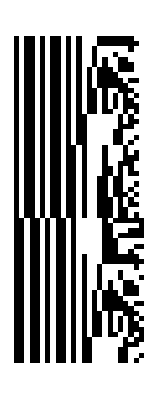

```mathematica
ArrayPlot[Map[IntegerDigits[#,2]&,Sort[DeleteDuplicates[Out[104]]]]]
```

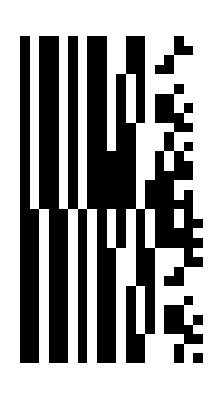

```mathematica
ArrayPlot[Map[IntegerDigits[#,2]&,Sort[DeleteDuplicates[Out[99]]]]]
```

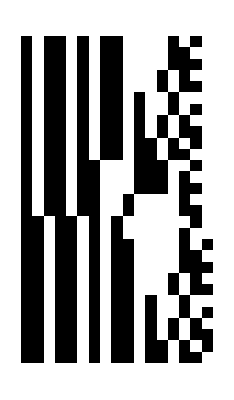

```mathematica
ArrayPlot[Map[IntegerDigits[#,2]&,Sort[DeleteDuplicates[Out[91]]]]]
```

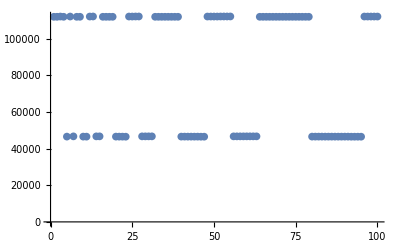

```mathematica
ListPlot[Out[89]]
```

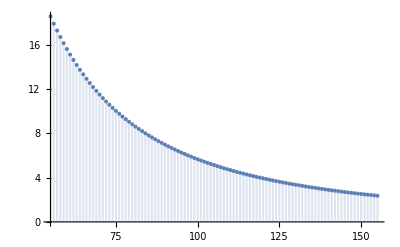

```mathematica
DiscretePlot[test[n],{n,55,155}]
```

```mathematica
Mean[{131071,54957,29671,12642,7998,3354,1807,773,508,215,115,49,31,13,7,3,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]//N
```

1610.7

```mathematica
Mean[{131071,54957,29671,12642,7998,3354,1807,773,508,215,115,49,31,13,7,3,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]//N
```

4768.92